(1 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | α | 1 | α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α | 1 | α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | α | 1 | α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | α | 1 | α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 1)

(0 | a/2 | b/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a/2 | 0 | a/2 | b/4 | 0 | 0 | 0 | 0 | 0 | 0
-b/4 | -a/2 | 0 | a/2 | b/4 | 0 | 0 | 0 | 0 | 0
0 | -b/4 | -a/2 | 0 | a/2 | b/4 | 0 | 0 | 0 | 0
0 | 0 | -b/4 | -a/2 | 0 | a/2 | b/4 | 0 | 0 | 0
0 | 0 | 0 | -b/4 | -a/2 | 0 | a/2 | b/4 | 0 | 0
0 | 0 | 0 | 0 | -b/4 | -a/2 | 0 | a/2 | b/4 | 0
0 | 0 | 0 | 0 | 0 | -b/4 | -a/2 | 0 | a/2 | b/4
0 | 0 | 0 | 0 | 0 | 0 | -b/4 | -a/2 | 0 | a/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -b/4 | -a/2 | 0)

(1 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/12 | 1 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/12 | 1 | -1/12 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/12 | 1 | -1/12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/12 | 1 | -1/12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/12 | 1 | -1/12 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/12 | 1 | -1/12 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/12 | 1 | -1/12 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/12 | 1 | -1/12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/12 | 1)

(0 | 8/9 | -17/72 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-8/9 | 0 | 8/9 | -17/72 | 0 | 0 | 0 | 0 | 0 | 0
17/72 | -8/9 | 0 | 8/9 | -17/72 | 0 | 0 | 0 | 0 | 0
0 | 17/72 | -8/9 | 0 | 8/9 | -17/72 | 0 | 0 | 0 | 0
0 | 0 | 17/72 | -8/9 | 0 | 8/9 | -17/72 | 0 | 0 | 0
0 | 0 | 0 | 17/72 | -8/9 | 0 | 8/9 | -17/72 | 0 | 0
0 | 0 | 0 | 0 | 17/72 | -8/9 | 0 | 8/9 | -17/72 | 0
0 | 0 | 0 | 0 | 0 | 17/72 | -8/9 | 0 | 8/9 | -17/72
0 | 0 | 0 | 0 | 0 | 0 | 17/72 | -8/9 | 0 | 8/9
0 | 0 | 0 | 0 | 0 | 0 | 0 | 17/72 | -8/9 | 0)

23032008169/139314069504+(147129403707376685 λ^2)/34665798542819328+(5297193419472605 λ^4)/361102068154368+(214410216060103 λ^6)/13374150672384+(207531719671 λ^8)/30958682112+(58130412911 λ^10)/61917364224

{0.+1.77698 ⅈ,0.-1.77698 ⅈ,0.+1.50627 ⅈ,0.-1.50627 ⅈ,0.+1.11056 ⅈ,0.-1.11056 ⅈ,0.+0.659173 ⅈ,0.-0.659173 ⅈ,0.+0.214165 ⅈ,0.-0.214165 ⅈ}

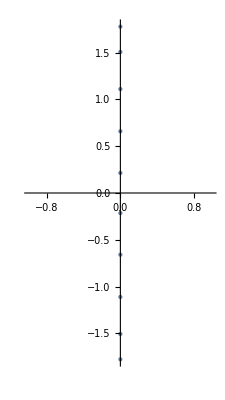

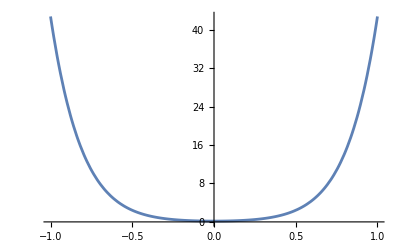

```mathematica
Clear["`*"];

size = 10;

triRowsLHS[i_,j_,α_,n_]:=Module[{},
If[i-1==j,α,
If[i==j,1,
If[i+1==j,α,0]
]
]
]

triRowsRHS[i_,j_,a_,b_,n_]:=Module[{},
(*If[i==1&&j==2,1,
If[i==n&&j==n-1,-1,*)
If[i-2==j,-b/4,
If[i+2==j,b/4,
If[i-1==j,-a/2,
If[i+1==j,a/2,0]
]
]
]
](*]]*)

(*Generate 5x5 LHS and RHS Matrices*)
LHS[k_]:=Array[triRowsLHS[#1,#2,α,k]&,{k,k}];
RHS[k_]:=Array[triRowsRHS[#1,#2,a,b,k]&,{k,k}];
LHS[size]//MatrixForm
RHS[size]//MatrixForm
LHSMat=LHS[size]/.{α->-1/12};
RHSMat=RHS[size]/.{a->16/9,b->-17/18};
LHSMat//MatrixForm
RHSMat//MatrixForm

characteristicPolynomial=Det[RHSMat-λ LHSMat]//FullSimplify//Expand

eig=Eigenvalues[Inverse[LHSMat].RHSMat]//N
ComplexListPlot[eig,PlotStyle->{PointSize->Medium}]
Plot[characteristicPolynomial,{λ,-1,1}]
```